## k=2, M=0

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
k=2;
nmax=4;
```

```mathematica
Table[(
trρ[n]=Import[StringJoin["k",ToString[k],"_server/210120_trrho_k",ToString[k],"_n",ToString[n],".m"]]//Expand;
),{n,1,nmax}];
```

```mathematica
(**)
(*
Subscript[Σ, N] z^N*Z(N)=Ξ(z)=Exp[1/2 Tr[Log[1+zρ]]]=Subscript[Σ, n] e^(J(μ+2πin)),
J=C/3 μ^3+Bμ+A+O(e^(-(...)μ))
*)
(**)
```

```mathematica
Clear[f];
CoefficientList[(Normal[Series[Exp[1/2*Sum[(-1)^(n-1)/n*z^n*f[n],{n,1,7}]],{z,0,nmax}]]//Expand),z]
```

{1,f[1]/2,f[1]^2/8-f[2]/4,f[1]^3/48-1/8 f[1] f[2]+f[3]/6,f[1]^4/384-1/32 f[1]^2 f[2]+f[2]^2/32+1/12 f[1] f[3]-f[4]/8}

```mathematica
Table[(
f[n]=trρ[n];
),{n,1,nmax}];
zZN={1,f[1]/2,f[1]^2/8-f[2]/4,f[1]^3/48-1/8 f[1] f[2]+f[3]/6,f[1]^4/384-1/32 f[1]^2 f[2]+f[2]^2/32+1/12 f[1] f[3]-f[4]/8}//Expand;
zZNlist=Table[{i-1,zZN[[i]]},{i,1,nmax+1}];
```

```mathematica
zZN[[1+1]]
zZN[[2+1]]
zZN[[3+1]]
zZN[[4+1]]
```

1/128

35/262144-1/(768 π^2)

313/33554432-1/(98304 π^2)-41/(1572864 π)

124679/274877906944+1/(1179648 π^4)-212743/(105696460800 π^2)-817/(1006632960 π)

```mathematica
N[zZNlist,3]
```

{{0,1.},{1.,0.00781},{2.,1.59×10^-6},{3.,1.95×10^-11},{4.,2.38×10^-17}}

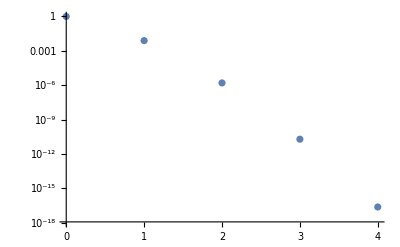

```mathematica
ListLogPlot[zZNlist]
```

```mathematica
(*airy:*)
aABJM[kk_]:=If[EvenQ[kk],
-Zeta[3]/(π^2*kk)-2/kk*Sum[m*(kk/2-m)*Log[2*Sin[(2*π*m)/kk]],{m,1,kk/2-1}],
-Zeta[3]/(8*π^2*kk)+kk/4*Log[2]-1/kk*Sum[(kk+(-1)^m*(2*m-kk))/4*(kk-(kk+(-1)^m*(2*m-kk))/4)*Log[2*Sin[(2*π*m)/kk]],{m,1,kk-1}]
];
aA=1/2*(aABJM[6*k]+9*aABJM[2*k]);
cC=1/(3*π^2*k);
bB=(π^2*cC)/3-5/(18*k)+k/4;
(*
bB=(π^2*cC)/3-1/(3*k)+k/4;
*)
logZpert=Table[{nN,Exp[aA]*cC^(-1/3)*AiryAi[cC^(-1/3)*(nN-bB)]},{nN,0,nmax+1,0.01}];
```

```mathematica
range={{0,nmax+1},All};
imsize=400;
plot1=ListLogPlot[{zZNlist,logZpert,zZNlist},Joined->{False,True,False},PlotStyle->{ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]],ColorData[97,"ColorList"][[1]]},PlotMarkers->{{"●",10},"",{"●",10}},PlotRange->range,Frame->True,FrameLabel->{"N","Z_(2, 0)(N)"},PlotLegends->Placed[{"Z_(2, 0)(N)","e^AC^(-1/3)Ai[C^(-1/3)(N-B)]"},{0.75,0.8}],ImageSize->imsize]
```

-Graphics-

```mathematica
deviations=Table[{√nN,Abs[zZN[[nN+1]]/(Exp[aA]*cC^(-1/3)*AiryAi[cC^(-1/3)*(nN-bB)])-1]},{nN,0,nmax}];
```

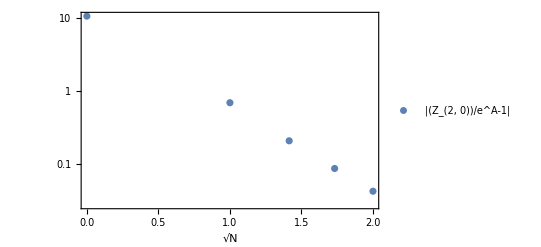

```mathematica
range=All;
(*
range={{0,nmax+1},All};
*)
imsize=400;
(*
origin={0,0};
*)
origin=Automatic;
plot2=ListLogPlot[deviations,AxesOrigin->origin,Frame->True,FrameLabel->{"√N",""},ImageSize->imsize,PlotLegends->Placed[{"|(Z_(2, 0))/e^A-1|"},{0.75,0.8}]]
```

```mathematica
Row[{plot1,plot2}]
```

-Graphics--Graphics-

```mathematica
Export["210122_affineD3_Z_vs_Airy_k2_M0.pdf",Style[%,LineBreakWithin->False]];
```

## k=3, M=0

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
k=3;
nmax=3;
```

```mathematica
Table[(
trρ[n]=Import[StringJoin["k",ToString[k],"_server/210120_trrho_k",ToString[k],"_n",ToString[n],".m"]]//Expand;
),{n,1,nmax}];
```

```mathematica
(**)
(*
Subscript[Σ, N] z^N*Z(N)=Ξ(z)=Exp[1/2 Tr[Log[1+zρ]]]=Subscript[Σ, n] e^(J(μ+2πin)),
J=C/3 μ^3+Bμ+A+O(e^(-(...)μ))
*)
(**)
```

```mathematica
Clear[f];
CoefficientList[(Normal[Series[Exp[1/2*Sum[(-1)^(n-1)/n*z^n*f[n],{n,1,7}]],{z,0,nmax}]]//Expand),z]
```

{1,f[1]/2,f[1]^2/8-f[2]/4,f[1]^3/48-1/8 f[1] f[2]+f[3]/6}

```mathematica
Table[(
f[n]=trρ[n];
),{n,1,nmax}];
zZN={1,f[1]/2,f[1]^2/8-f[2]/4,f[1]^3/48-1/8 f[1] f[2]+f[3]/6}//ComplexExpand;
zZNlist=Table[{i-1,zZN[[i]]},{i,1,nmax+1}];
```

```mathematica
zZN[[1+1]]
zZN[[2+1]]
zZN[[3+1]]
```

1/192

-883/10077696+1/(1152 π^2)

-7172861/1671768834048+89/(9953280 π^2)+29/(1574640 √3 π)

```mathematica
N[zZNlist,3]
```

{{0,1.},{1.,0.00521},{2.,3.33×10^-7},{3.,6.66×10^-13}}

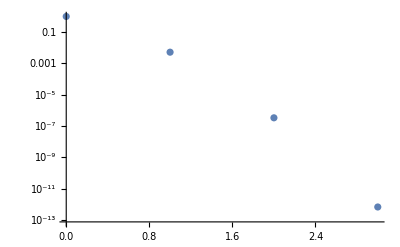

```mathematica
ListLogPlot[zZNlist]
```

```mathematica
(*airy:*)
aABJM[kk_]:=If[EvenQ[kk],
-Zeta[3]/(π^2*kk)-2/kk*Sum[m*(kk/2-m)*Log[2*Sin[(2*π*m)/kk]],{m,1,kk/2-1}],
-Zeta[3]/(8*π^2*kk)+kk/4*Log[2]-1/kk*Sum[(kk+(-1)^m*(2*m-kk))/4*(kk-(kk+(-1)^m*(2*m-kk))/4)*Log[2*Sin[(2*π*m)/kk]],{m,1,kk-1}]
];
aA=1/2*(aABJM[6*k]+9*aABJM[2*k]);
cC=1/(3*π^2*k);
bB=(π^2*cC)/3-5/(18*k)+k/4;
(*
bB=(π^2*cC)/3-1/(3*k)+k/4;
*)
logZpert=Table[{nN,Exp[aA]*cC^(-1/3)*AiryAi[cC^(-1/3)*(nN-bB)]},{nN,0,nmax+1,0.01}];
```

```mathematica
range={{0,nmax+1},All};
imsize=400;
plot1=ListLogPlot[{zZNlist,logZpert,zZNlist},Joined->{False,True,False},PlotStyle->{ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]],ColorData[97,"ColorList"][[1]]},PlotMarkers->{{"●",10},"",{"●",10}},PlotRange->range,Frame->True,FrameLabel->{"N","Z_(3, 0)(N)"},PlotLegends->Placed[{"Z_(3, 0)(N)","e^AC^(-1/3)Ai[C^(-1/3)(N-B)]"},{0.75,0.8}],ImageSize->imsize]
```

-Graphics-

```mathematica
deviations=Table[{√nN,Abs[zZN[[nN+1]]/(Exp[aA]*cC^(-1/3)*AiryAi[cC^(-1/3)*(nN-bB)])-1]},{nN,0,nmax}];
```

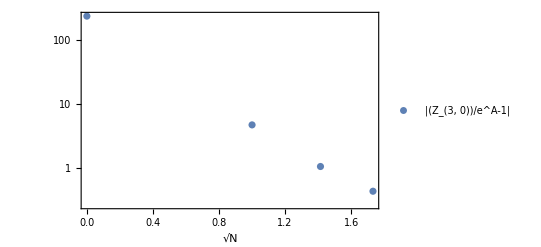

```mathematica
range=All;
(*
range={{0,nmax+1},All};
*)
imsize=400;
(*
origin={0,0};
*)
origin=Automatic;
plot2=ListLogPlot[deviations,AxesOrigin->origin,Frame->True,FrameLabel->{"√N",""},ImageSize->imsize,PlotLegends->Placed[{"|(Z_(3, 0))/e^A-1|"},{0.75,0.8}]]
```

```mathematica
Row[{plot1,plot2}]
```

-Graphics--Graphics-

```mathematica
Export["210122_affineD3_Z_vs_Airy_k3_M0.pdf",Style[%,LineBreakWithin->False]];
```